### Configuration

```mathematica
cfg={pr->1.*10^5,Dw->0.1,mu->0.001,Kvw->1.*10^-12,qin->-0.05065050785314778,rho->1000.0};
Reynolds=(rho Abs[qin] Dw)/mu/.cfg
```

5065.05

### Q space

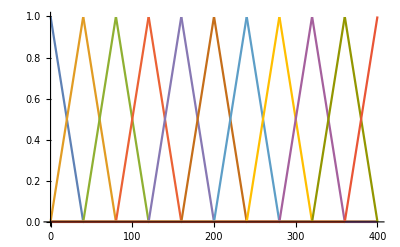

```mathematica
domainsize=400;
nel=10;
xco=Table[(i-1) domainsize/nel,{i,0,nel+2}];
hatfunc[xco_,x_]:=Table[Piecewise[{{0,x<xco[[i]]},{(x-xco[[i]])/(xco[[i+1]]-xco[[i]]),x<xco[[i+1]]},{(xco[[i+2]]-x)/(xco[[i+2]]-xco[[i+1]]),x<xco[[i+2]]}},0],{i,1,Length[xco]-2}]
qphi=hatfunc[xco,x];
dqphi=D[qphi,x];
Plot[{qphi},{x,0,domainsize},PlotRange->All]
```

### P space

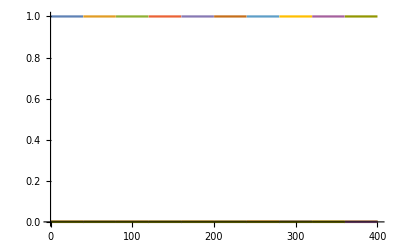

```mathematica
ctefunc[xco_,x_]:=Table[Piecewise[{{0,x<xco[[i]]},{1,x<xco[[i+1]]}},0],{i,1,Length[xco]-2}]
pphi=ctefunc[xco[[2;;-1]],x];
Plot[pphi,{x,0,domainsize},PlotRange->All]
```

### Matrix and vector

```mathematica
ndofsp=Length[pphi];
ndofsq=Length[qphi];
ndofs=ndofsp+ndofsq;
Kg=ConstantArray[0,{ndofs,ndofs}];
Fg=ConstantArray[0,{ndofs}];
Kg[[1;;ndofsq,1;;ndofsq]]=(128 mu)/(Dw^4 π)Table[Integrate[qphi[[i]]qphi[[j]],{x,0,domainsize}],{i,ndofsq},{j,ndofsq}];
Kg[[1;;ndofsq,ndofsq+1;;-1]]=-Table[Integrate[dqphi[[i]]pphi[[j]],{x,0,domainsize}],{i,ndofsq},{j,ndofsp}];
Kg[[ndofsq+1;;,1;;ndofsq]]=Transpose[Kg[[1;;ndofsq,ndofsq+1;;-1]]];
Kg[[ndofsq+1;;,ndofsq+1;;]]=-Kvw Table[Integrate[pphi[[i]]pphi[[j]],{x,0,domainsize}],{i,ndofsp},{j,ndofsp}];
Fg[[ndofsq+1;;]]=-Kvw pr Table[Integrate[pphi[[i]],{x,0,domainsize}],{i,ndofsp}];
Fg[[1]]-=-10;
Kg=Kg/.cfg;
Fg=Fg/.cfg;
a=LinearSolve[Kg,Fg]//Simplify;
Kg//MatrixForm
Fg//MatrixForm
a
```

(5432.49 | 2716.24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
2716.24 | 10865. | 2716.24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 2716.24 | 10865. | 2716.24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2716.24 | 10865. | 2716.24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 2716.24 | 10865. | 2716.24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 2716.24 | 10865. | 2716.24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 2716.24 | 10865. | 2716.24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2716.24 | 10865. | 2716.24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2716.24 | 10865. | 2716.24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2716.24 | 10865. | 2716.24 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2716.24 | 5432.49 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4.×10^-11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4.×10^-11 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4.×10^-11 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4.×10^-11 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4.×10^-11 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4.×10^-11 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4.×10^-11 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4.×10^-11 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4.×10^-11 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -4.×10^-11)

(10
0
0
0
0
0
0
0
0
0
0
-4.×10^-6
-4.×10^-6
-4.×10^-6
-4.×10^-6
-4.×10^-6
-4.×10^-6
-4.×10^-6
-4.×10^-6
-4.×10^-6
-4.×10^-6)

{0.0000413607,0.0000453603,0.0000493599,0.0000533596,0.0000573593,0.0000613591,0.0000653588,0.0000693587,0.0000733586,0.0000773585,0.0000813585,9.6521,8.91284,8.1084,7.23877,6.30396,5.30396,4.23878,3.10841,1.91285,0.652103}

### Plotting solution

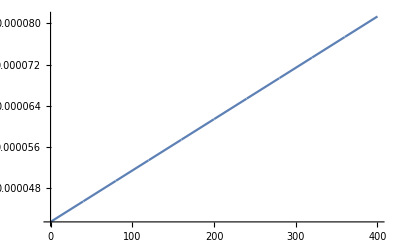

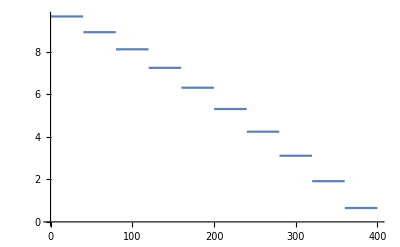

```mathematica
solq=a[[;;ndofsq]].qphi;
solp=a[[ndofsq+1;;]].pphi;
Plot[solq,{x,0,domainsize}]
Plot[solp,{x,0,domainsize}]
```

### Non linear

```mathematica
Qnodal=a[[;;ndofsq]];
Qcurr=Qnodal.qphi;
Plot[Qcurr,{x,0,domainsize}]
c=(2.252610888 Dw^(19/7))/(mu^(1/7)rho^(3/7));
d=c^(-7/4)/.cfg;
d/.cfg
```

-Graphics-

429338.

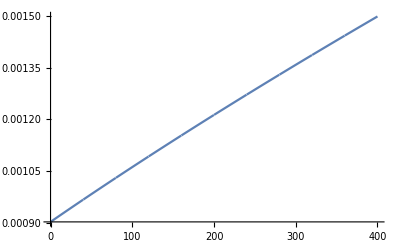

```mathematica
Plot[((Abs[Qcurr])^(3/4)+(3 Abs[Qcurr]^(3/4))/4),{x,0,domainsize}]
```

```mathematica
maxsteps=4;
pnodal=ConstantArray[0,{ndofsp}];
Kg=ConstantArray[0,{ndofs,ndofs}];
Fg=ConstantArray[0,{ndofs}];
For[i=1,i<=maxsteps,i++,
Print["-------- Iteration ",i," ---------"];
Qcurr=Qnodal.qphi/.cfg;
pcurr=pnodal.pphi/.cfg;
dQcurr=D[Qcurr,x];

Kg[[1;;ndofsq,1;;ndofsq]]=Table[NIntegrate[d ((Abs[Qcurr])^(3/4)+(3 Abs[Qcurr]^(3/4))/4)qphi[[i]]qphi[[j]],{x,0,domainsize}],{i,ndofsq},{j,ndofsq}];
Kg[[1;;ndofsq,ndofsq+1;;-1]]=-Table[Integrate[dqphi[[i]]pphi[[j]],{x,0,domainsize}],{i,ndofsq},{j,ndofsp}];
Kg[[ndofsq+1;;,1;;ndofsq]]=Transpose[Kg[[1;;ndofsq,ndofsq+1;;-1]]];
Kg[[ndofsq+1;;,ndofsq+1;;]]=-Kvw Table[Integrate[pphi[[i]]pphi[[j]],{x,0,domainsize}],{i,ndofsp},{j,ndofsp}]/.cfg;
Fg[[1;;ndofsq]]= Table[Integrate[d Qcurr Abs[Qcurr]^(3/4) qphi[[i]]-dqphi[[i]]pcurr,{x,0,domainsize}],{i,ndofsq}]/.cfg;
Fg[[ndofsq+1;;]]= Table[Integrate[-pphi[[i]] dQcurr-Kvw pphi[[i]]pcurr+Kvw pphi[[i]]pr,{x,0,domainsize}],{i,ndofsp}]/.cfg;
Fg[[1]]+=-10;

(*Print["Kg = ",Kg//MatrixForm];*)
Kg=Kg/.cfg;
Fg=Fg/.cfg;

normF=Norm[Fg];
Print["normF = ",normF];
If[normF<10^-3,Print["Converged with normF = ",normF];Break[]];

da=LinearSolve[Kg,-Fg];
normda=Norm[da];
If[normda<10^-4,Print["Converged with normda = ",normda];Break[]];
(*Print["da = ",da];*)
Print["normda = ",Norm[da]];

Qnodal+=da[[;;ndofsq]];
pnodal+=da[[ndofsq+1;;]];
(*Print["Qnodal = ",Qnodal];
Print["pnodal = ",pnodal];*)
]
```

-------- Iteration 1 ---------

normF = 10.0949

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{5259.98,2676.39,0.,0.,0.,0.,0.,0.,0.,0.,«11»},{2676.39,11073.4,2859.51,0.,0.,0.,0.,0.,0.,0.,«11»},{0.,2859.51,11798.,3038.79,0.,0.,0.,0.,0.,0.,«11»},{0.,0.,3038.79,12508.1,3214.62,0.,0.,0.,0.,0.,«11»},«4»,{0.,0.,0.,0.,0.,0.,0.,3888.88,15881.2,4051.25,«11»},{0.,0.,0.,0.,0.,0.,0.,0.,4051.25,16526.3,«11»},«11»} may contain significant numerical errors.

normda = 20.4608

-------- Iteration 2 ---------

normF = 0.0574209

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{6355.81,3221.5,0.,0.,0.,0.,0.,0.,0.,0.,«11»},{3221.5,13232.3,3394.05,0.,0.,0.,0.,0.,0.,0.,«11»},{0.,3394.05,13916.7,3563.73,0.,0.,0.,0.,0.,0.,«11»},{0.,0.,3563.73,14590.,3730.75,0.,0.,0.,0.,0.,«11»},«4»,{0.,0.,0.,0.,0.,0.,0.,4375.9,17816.9,4532.16,«11»},{0.,0.,0.,0.,0.,0.,0.,0.,4532.16,18438.3,«11»},«11»} may contain significant numerical errors.

normda = 0.0303277

-------- Iteration 3 ---------

normF = 0.000230748

Converged with normF = 0.000230748

### Plotting solution

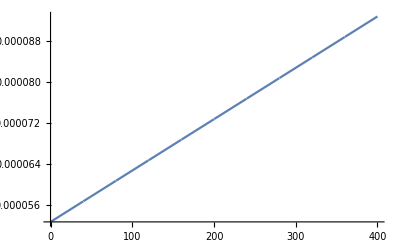

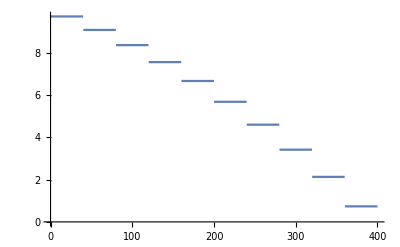

```mathematica
solq=Qnodal.qphi;
solp=pnodal.pphi;
Plot[solq,{x,0,domainsize}]
Plot[solp,{x,0,domainsize}]
```